## Lab 1: Carter Colton Assignment 0: Basic Calculations

Assignment 0:  Basic computation (You should do this, but it won’t be graded.)
In a new notebook do these computations. It might be good to check your answer against your calculator.
(a)  √(1+(2/(3-log_10 4)))  (give the answer to 10 sig figs)
(b) the answer to (a) + ln(2.39).

```mathematica
N[Sqrt[1+(2/(3-Log10[4]))],10]
```

1.354270735

```mathematica
%+Log[2.39]
```

2.22556

## Assignment 1: Position is the Integral of Velocity

```mathematica
Define a function of time: v(t) = v0 - g t, where v0 is a variable defined to be 5 and g is a variable defined to be 9.8. Define x(t) to be the integral of that function. Plot both v(t) and x(t) on same graph with different colors, for t = 0 to 2.
```

Define a function of time: v(t) = v0 - g t, where v0 is a variable defined to be 5 and g is a variable defined to be 9.8. Define x(t) to be the integral of that function. Plot both v(t) and x(t) on same graph with different colors, for t = 0 to 2.

```mathematica
v0=5
g=9.8
```

5

9.8

```mathematica
v[t_]=v0-g*t
```

5-9.8 t

```mathematica
x[t_]=Integrate[v[t],t]
```

5 t-4.9 t^2

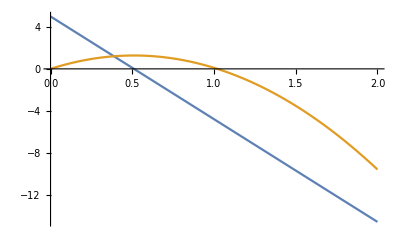

```mathematica
Plot[{v[t],x[t]},{t,0,2}]
```

## Assignment 2: Solving an Equation, Numerically

```mathematica
For what value of x (in radians) does cos(x) = x?  
(a) Start by plotting cos(x) and x on the same graph. You can get an approximate answer by looking at where the two curves intersect: that’s where cos(x) equals x. 
(b) Then use FindRoot to get a precise answer.
```

For what value of x (in radians) does cos(x) = x?  
(a) Start by plotting cos(x) and x on the same graph. You can get an approximate answer by looking at where the two curves intersect: that’s where cos(x) equals x. 
(b) Then use FindRoot to get a precise answer.

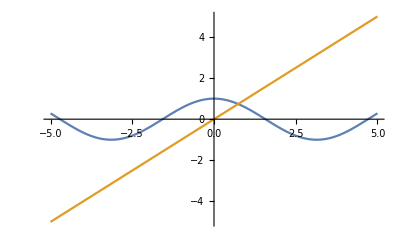

```mathematica
Plot[{Cos[x], x}, {x,-5,5}]
```

```mathematica
FindRoot[Cos[x] == x, {x, 0.5}]
```

{x→0.739085}

## Assignment 3: Diffraction From a Slit

```mathematica
In Physics 123 you hopefully learned that the diffraction pattern produced by a single slit of non-negligible width is given by:  I(x) = Subscript[I, 0]  ((sin(πxa/λL))/(πxa/λL))^2, where a is the slit width, L is the distance to the screen where the pattern is being observed, and x is the position on the screen.  (Disclaimer: this involves a small angle approximation.) Sometimes that equation is written in terms of the "sinc" function, where sinc(x)=(sin(x))/x. (Incidentally, Sinc is a pre-defined function in Mathematica, just like Sin itself.) In the equation, Subscript[I, 0] is the intensity at x = 0, i.e. the mid-point of the diffraction pattern; let's just define that as 1 for simplicity.
(a) Make a plot of this function for a few maxima/minima around the central maximum, for a 100 micron slit, a 633 nm laser, and a distance to screen = 10 m. Make two plots, actually: one with the default y-axis (meaning intensity)  range, and a second one where you use a PlotRange option to “zoom out” and fully see the central peak.
(b) Determine the position of the first maximum to the right of the central maximum. Side note: In Physics 123 you learned a simple formula for the minima, but there is no similar simple formula for the maxima. They are only approximately located equidistant between the minima.
```

Set::write: Tag Times in ⅈ x is Protected.

Set::write: Tag Times in sinc x is Protected.

Unset::norep: Assignment on Annotation for MakeBoxes[BoxForm`apat$:HoldPattern[___],BoxForm`fpat$_] not found.

Unset::norep: Assignment on Deploy for MakeBoxes[BoxForm`apat$:HoldPattern[___],BoxForm`fpat$_] not found.

Unset::norep: Assignment on DynamicImage for MakeBoxes[BoxForm`apat$:HoldPattern[],BoxForm`fpat$_] not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

TagUnset::norep: Assignment on FrameBox for BoxForm`apat$:HoldPattern[MakeExpression[_FrameBox,_]] not found.

TagUnset::norep: Assignment on ItemBox for BoxForm`apat$:HoldPattern[MakeExpression[_ItemBox,_]] not found.

TagUnset::norep: Assignment on PaneBox for BoxForm`apat$:HoldPattern[MakeExpression[_PaneBox,_]] not found.

General::stop: Further output of TagUnset::norep will be suppressed during this calculation.

In Physics 123 you hopefully learned that the diffraction pattern produced by a single slit of non-negligible width is given by:  ⅈ_0 sin^2, where a is the slit width, L is the distance to the screen where the pattern is being observed, and x is the position on the screen.  (Disclaimer: this involves a small angle approximation.) Sometimes that equation is written in terms of the "sinc" function, where sin. (Incidentally, Sinc is a pre-defined function in Mathematica, just like Sin itself.) In the equation, ⅈ_0 is the intensity at x = 0, i.e. the mid-point of the diffraction pattern; let's just define that as 1 for simplicity.
(a) Make a plot of this function for a few maxima/minima around the central maximum, for a 100 micron slit, a 633 nm laser, and a distance to screen = 10 m. Make two plots, actually: one with the default y-axis (meaning intensity)  range, and a second one where you use a PlotRange option to “zoom out” and fully see the central peak.
(b) Determine the position of the first maximum to the right of the central maximum. Side note: In Physics 123 you learned a simple formula for the minima, but there is no similar simple formula for the maxima. They are only approximately located equidistant between the minima.

```mathematica
i0=1
a=100*^-6
lamda=633*^-9
L=10
```

1

1/10000

633/1000000000

10

```mathematica
i[x_] = i0*((Sin[((Pi*x*a)/(lamda*L))])/((Pi*x*a)/(lamda*L)))^2
```

(400689 Sin[(10000 π x)/633]^2)/(100000000 π^2 x^2)

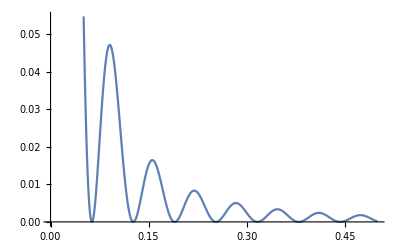

```mathematica
Plot[i[x], {x, 0, .5}]
```

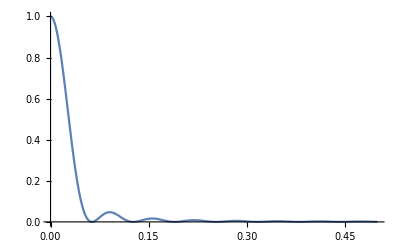

```mathematica
Plot[i[x], {x, 0, .5}, PlotRange -> All]
```

```mathematica
FindMaximum[i[x], x]
```

{0.00042191,{x→0.980736}}

## Assignment 4: Two Summations

```mathematica
(a) Calculate the value of  ∑_(n=1)^∞ 1/n^6, in both symbolic and numerical form. 
(b) Calculate the value of 1 - 1/2 + 1/3 - 1/4 + 1/5 - 1/6 + ...
```

(a) Calculate the value of  π^6/945, in both symbolic and numerical form. 
(b) Calculate the value of 1 - 1/2 + 1/3 - 1/4 + 1/5 - 1/6 + ...

```mathematica
Sum[1/(n^6), {n,1,Infinity}]
```

π^6/945

```mathematica
N[%]
```

1.01734

```mathematica
Sum[(-1)^n/(n+1),{n,0,Infinity}]
```

Log[2]

```mathematica
N[%]
```

0.693147

## Assignment 5: The Plot Thickens

```mathematica
Make a plot of x^4 + 2 x^3 +3 x^2+ 4 x+5, from x = -3 to x = 3. Experiment with different plot styles as options, such as PlotStyle→Thick,  or PlotStyle→Red (or Blue, or Green, or Magenta, etc.), or PlotStyle→Dashed  (or Dotted, or DotDashed), or PlotStyle→Opacity[0.5] (or Opacity[0.1], or Opacity[0.8], etc.). After you have experimented a bit with these options, choose your favorite plot styles and combine them together via a list enclosed in braces: PlotStyle→{option1, option2, option3, etc.}.
```

Make a plot of x^4+2 x^3+3 x^2+4 x+5, from x = -3 to x = 3. Experiment with different plot styles as options, such as PlotStyle→Thick,  or PlotStyle→Red (or Blue, or Green, or Magenta, etc.), or PlotStyle→Dashed  (or Dotted, or DotDashed), or PlotStyle→Opacity[0.5] (or Opacity[0.1], or Opacity[0.8], etc.). After you have experimented a bit with these options, choose your favorite plot styles and combine them together via a list enclosed in braces: PlotStyle→{option1, option2, option3, etc.}.

```mathematica
f[x_]=x^4+2*x^3+3*x^2+4*x+5
```

5+4 x+3 x^2+2 x^3+x^4

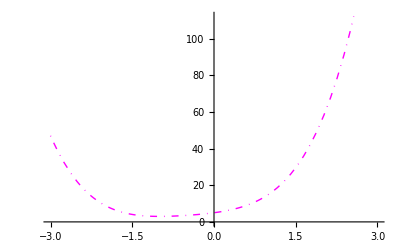

```mathematica
Plot[f[x], {x, -3, 3}, PlotStyle->{Thick,Magenta,DotDashed,Opacity[1]}]
```

## Assignment 6: Polynomial Roots

As you should have just seen from the plot, the polynomial x^4 + 2 x^3 + 3 x^2 + 4 x + 5 has no real roots. (It doesn' t cross zero anywhere.) It does, however, have four complex roots. What are they? Find them in decimal form.

```mathematica
Solve[f[x]==0,x]
```

{{x→Root-1.29-0.858 ⅈRoot[5+4 #1+3 #1^2+2 #1^3+#1^4&,1]-1.287815479557648},{x→Root-1.29+0.858 ⅈRoot[5+4 #1+3 #1^2+2 #1^3+#1^4&,2]-1.287815479557648},{x→Root0.288-1.42 ⅈRoot[5+4 #1+3 #1^2+2 #1^3+#1^4&,3]0.28781547955764797},{x→Root0.288+1.42 ⅈRoot[5+4 #1+3 #1^2+2 #1^3+#1^4&,4]0.28781547955764797}}

## Assignment 7: Taylor Series of e^x

The Taylor’s series of e^x evaluated at x = 1 is 1 + 1 + 1/2 + 1/3! + 1/4!  + ... .  Show that this series gets closer and closer to the true value of e  (=e^1) as you include more and more terms. Try 5 terms (as shown), 10 terms, and 100 terms; give your results to 50 decimal places. Also display e to 50 decimal places for comparison.

```mathematica
1+Sum[(1/(n!)),{n,1,5}]
```

163/60

```mathematica
N[%,50]
```

2.7166666666666666666666666666666666666666666666667

```mathematica
1+Sum[(1/(n!)),{n,1,10}]
```

9864101/3628800

```mathematica
N[%,50]
```

2.7182818011463844797178130511463844797178130511464

```mathematica
1+Sum[(1/(n!)),{n,1,100}]
```

4299778907798767752801199122242037634663518280784714275131782813346597523870956720660008227544949996496057758175050906671347686438130409774741771022426508339/1581800261761765299689817607733333906622304546853925787603270574495213559207286705236295999595873191292435557980122436580528562896896000000000000000000000000

```mathematica
N[%,50]
```

2.7182818284590452353602874713526624977572470937

```mathematica
2.71828182845904523536028747135266249775724709369995957496696828199217637781302`50.
E
```

2.7182818284590452353602874713526624977572470937

ⅇ

```mathematica
N[%,50]
```

2.7182818284590452353602874713526624977572470937

## Assignment 8: A Basic Derivative

Define the function f8(x) = (sin^2(x))/(1+cos(x)). Take its derivative, and simplify the result.

```mathematica
f8[x_]=(Sin[x]^2)/(1+Cos[x])
```

Sin[x]^2/(1+Cos[x])

```mathematica
f8'[x]
```

(2 Cos[x] Sin[x])/(1+Cos[x])+Sin[x]^3/(1+Cos[x])^2

```mathematica
Simplify[%]
```

Sin[x]

## Assignment 9: A Basic Integral

Determine  ∫e^-x sin(x)ⅆx, integrated from 0 to infinity.

```mathematica
Clear[g]
```

```mathematica
g[x_]=(E^-x)*Sin[x]
```

ⅇ^-x Sin[x]

```mathematica
Integrate[g[x],{x,0,Infinity}]
```

1/2

```mathematica
N[%]
```

0.5

## Assignment 10: A Basic Complex Number Calculation

Do a search in Mathematica's help files to find the "Complex numbers tutorial". Pay special attention to the Abs and Arg commands. Use them to calculate the magnitude and angle (in radians) of:  (4 + 5i) ÷ (6 - 7i).  Give your answers in decimal form to 8 sig figs.

```mathematica
(4+5I)/(6-7I)
```

-11/85+(58 ⅈ)/85

```mathematica
Abs[%]
```

√(41/85)

```mathematica
(4+5I)/(6-7I)
```

-11/85+(58 ⅈ)/85

```mathematica
Arg[%]
```

π-ArcTan[58/11]

```mathematica
N[%,8]
```

1.7582254